```mathematica
Quit
```

## Definitions

```mathematica
ξ=ⅇ^((2ⅈ π)/3);
mandelstamRules={s->(-3z p2)/(z^2+z+1),t->(-3ξ z p2)/((ξ z)^2+ξ z+1),u->(-3 ξ^2 z p2)/((ξ^2 z)^2+ξ^2 z+1)};
xsymmetricrules={z->(t^2+u^2-2 s^2-ⅈ √3 s(t-u))/(s^2+t^2+u^2),p2->(2 s t u)/(s^2+t^2+u^2)};
IRAmp[nmax_Integer,z_,p2_]:=g0+∑_(p=1)^(nmax/2) ∑_(q=0)^Min[p,nmax-2p] Subscript[g, 2p+q,q] p2^(2p+q) (-(27 z^3)/((z^3-1)^2))^p//Expand
zKernel[n_,z_,p2_]:=(-1)^n((z^3+1)(1-z^3)^(2n+1))/(2×3^(3+3n)p2^(2+2n)z^(4+3n))
sKernel[n_,s_,p2_]:=(3 p2+2 s)/s^(3n+4)(p2+s)^n
P[d_,l_]:=Hypergeometric2F1[-l,l+d-3,(d-2)/2,(1-#)/2]&
IRInt[n_,k_]:=D[Sum[Residue[zKernel[n,z,p2]IRAmp[10,z,p2],{z,ξ^i}],{i,0,2}],{p2,k}]/.p2->0
UVInt[n_,k_,d_,l_,s_]:=D[sKernel[n,s,p2]P[d,l][√((s-3p2)/(s+p2))],{p2,k}]/.p2->0//FullSimplify
EliminateLinearDependence[set_]:=If[Length@#>0,Delete[set,#[[1]]],set]&@(DeleteCases[x_->0]@Quiet@Solve[(#==0)&/@CoefficientList[Sum[α[i]set[[i]],{i,1,Length@set}],l],Table[α[i],{i,1,Length@set}]][[1]]/.(α[x_]->y_):>x)
ncIndices[n_Integer]:=Table[{m,n-2m},{m,0,Floor[(n-2)/3]}]/;n>=2
NullConstraints[d_Integer,n_Integer]:=FixedPoint[EliminateLinearDependence,UVInt[#[[1]],#[[2]],d,l,s]&/@ncIndices[n]]/;n>=2
```

```mathematica
IRInt2[n_,k_,d_]:=IRInt[n,k]-λ2 UVInt[n,k,d,2,1]//Simplify
UVg22[d_,l_,s_]:=UVInt[0,0,d,l,s]+(d-2)/(4(d-1))UVInt[0,2,d,l,s]
nonTrivialNC2[k_,d_]:=Module[{α},
α=a/.Solve[(IRInt2[0,2+k,d]+a IRInt2[0,3+k,d])/λ2==0//Simplify,a][[1]];
UVInt[0,2+k,d,l,s]+α UVInt[0,3+k,d,l,s]//Simplify
]/;k>=0
ncIndices2[n_Integer]:=Table[{m,n-2m},{m,1,Floor[(n-2)/3]}]/;n>=2
NullConstraints2[d_Integer,n_Integer]:=Join[EliminateLinearDependence[UVInt[#[[1]],#[[2]],d,l,s]&/@ncIndices2[n]],{nonTrivialNC2[n-3,d]}]/;n>=3
```

```mathematica
IRInt3[n_,k_,d_,μ4_]:=IRInt[n,k]-λ2 UVInt[n,k,d,2,1]-λ4 UVInt[n,k,d,4,μ4]//Simplify
UVg23[d_,l_,s_,μ4_]:=UVInt[0,0,d,l,s]+(-2+d)/(4 (-1+d))UVInt[0,2,d,l,s]-((-2+d) μ4^3 (6 (1+d) (4+d)+(-1+d) d μ4^2))/(48 (-1+d) (1+d) (3+d))UVInt[1,3,d,l,s]//FullSimplify
nonTrivialNC3[k_,d_]:=Module[{α},
α=a/.Solve[(IRInt3[1,3+k,d,μ4]+a IRInt3[1,4+k,d,μ4])/λ4==0//Simplify,a][[1]];
UVInt[1,3+k,d,l,s]+α UVInt[1,4+k,d,l,s]//Simplify
]/;k>=0
nonTrivialNC32[k_,d_]:=Module[{α,β},
{α,β}={a,b}/.Solve[{Coefficient[#,λ2]==0,Coefficient[#,λ4]==0}&[IRInt3[0,2+k,d,μ4]+a IRInt3[0,3+k,d,μ4]+b IRInt3[1,3+k,d,μ4]//Simplify],{a,b}][[1]];
UVInt[0,2+k,d,l,s]+α UVInt[0,3+k,d,l,s]+β UVInt[1,3+k,d,l,s]//Simplify
]/;k>=0
ncIndices3[n_Integer]:=Table[{m,n-2m},{m,2,Floor[(n-2)/3]}]/;n>=2
NullConstraints3[d_Integer,n_Integer,μ_]:=(DeleteCases[_[_,_]]@Join[EliminateLinearDependence[UVInt[#[[1]],#[[2]],d,l,s]&/@ncIndices3[n]],EliminateLinearDependence@{nonTrivialNC3[n-6,d],nonTrivialNC32[n-5,d]}]/.μ4->μ)/;n>=5
```

## SDPB (local)

```mathematica
$Assumptions=None;
<<SDPB`
```

```mathematica
ComputeBoundLocal[sign_Integer,name_String,precision_Integer:1024,ncores_Integer:$ProcessorCount]:=Module[{fullName,directory},
fullName=name<>If[sign==1,"Hi","Low"];
directory=FileNameJoin[{$TemporaryDirectory,fullName}];

(*create SDPB directory*)
If[FileExistsQ[directory],
ExternalEvaluate["Shell","docker run --rm -v "<>$TemporaryDirectory<>":/usr/local/toremove docker.io/bootstrapcollaboration/sdpb:master rm -r /usr/local/toremove/"<>fullName];
];
CreateDirectory[directory];
RenameFile[FileNameJoin[{$TemporaryDirectory,name<>".json"}],FileNameJoin[{directory,fullName<>".json"}]];

(*Write SDPB input file*)
ExternalEvaluate["Shell",ToString@StringForm["docker run --rm -v `4`:/usr/local/share/sdpb/ docker.io/bootstrapcollaboration/sdpb:master mpirun --allow-run-as-root -n `3` pmp2sdp `1` /usr/local/share/sdpb/`2`.json /usr/local/share/sdpb/`2`",precision,fullName,ncores,directory]];

ExternalEvaluate["Shell",ToString@StringForm["docker run --rm -v `4`:/usr/local/share/sdpb/ docker.io/bootstrapcollaboration/sdpb:master mpirun --allow-run-as-root -n `1` sdpb --noFinalCheckpoint --precision=`2` -s /usr/local/share/sdpb/`3` --maxSharedMemory=65MB",ncores,precision,fullName,directory]];
]
```

```mathematica
FetchBoundLocal[sign_Integer,name_String]:=Module[{fullName,fileName},
fullName=name<>If[sign==1,"Hi","Low"];
fileName=FileNameJoin[{$TemporaryDirectory,fullName,fullName<>"_out","out.txt"}];
-sign ExternalEvaluate["Python","import re
with open('"<>fileName<>"', 'r') as f:
	s = f.read()
float(re.findall(r'primalObjective = .*;', s)[0][len('primalObjective = '):-1])"]
]
```

```mathematica
GetBoundLocal[d_,μ2_,μ4_,μCut_,ncCount_,lmax_Integer,name_String,ncores_Integer:$ProcessorCount,precision_Integer:1024]:=Module[{},(*shorthand for prepare, compute*)
PrepareBound[d,μ2,μ4,μCut,ncCount,lmax,name,precision];
ComputeBoundLocal[1,name,precision,ncores];
FetchBoundLocal[1,name]
]
```

## SDPB (cluster+common)

```mathematica
$Assumptions=None;
<<SDPB`
```

```mathematica
User="ricossa";
Server="login1.baobab.hpc.unige.ch";
ServerDirectory="sdpbRun";
```

```mathematica
NearestNeighborSort[data_]:=Module[{res,data1,temp},
data1=data[[2;;]];
res={data[[1]]};
While[Length@data1!=0,
temp=Flatten@TakeSmallestBy[data1,(res[[-1,1]]-#[[1]])^2+(res[[-1,2]]-#[[2]])^2&,1];
AppendTo[res,temp];
data1=DeleteCases[data1,temp];
];
res
]
```

```mathematica
MatricesForSDPB[UVM_,lmax_Integer]:=SparseArray@Append[
Transpose[Quiet@ParallelTable[Join[
Table[Normal[UVM[[ii]]/.l->ll]//Expand,{ll,0,lmax,2}],
{Normal[UVM[[ii]]/.l->10^3 lmax]//Expand,Normal[UVM[[ii]]/.l->10^4 lmax]//Expand,Normal[UVM[[ii]]/.l->10^5 lmax]//Expand}
],{ii,1,Length@UVM}],{2,1}],
Normal@Series[UVM/.s->x l//Simplify,{l,∞,Series[Plus@@Flatten@UVM/.s->x l//Simplify,l->∞][[4]]}]/.l->1]
```

```mathematica
ComputeBound[name_String,nodes_Integer,tasksPerNode_Integer,time_String,fixedCoeff_List:{},hiOnly_Symbol:False,precision_Integer:1024]:=Module[{fullPath,command},
If[RunProcess[{"ssh", User<>"@"<>Server, "[ -f "<>ServerDirectory<>"/lock ]"},"ExitCode"]==0,
Print["An operation is still pending.... CheckStatus[] for more information. Manually delete "<>ServerDirectory<>"/lock if the problem persists."];
Abort[];
];
fullPath=FileNameJoin@{$TemporaryDirectory,name<>".json"};
command=ToString@StringForm["cd "<>ServerDirectory<>" && sbatch --nodes=`1` --ntasks-per-node=`2` --time="<>time<>" sdpb.sh --precision=`3` ",nodes,tasksPerNode,precision];
If[Length@fixedCoeff>0,
command=command<> "--fixed_coeff="<>StringDrop[StringJoin@@(ToString[DecimalForm@#]<>","&/@fixedCoeff),-1]<>" ";
];
If[hiOnly,command=command<>"--hi_only ";];
command=command<>name<>".json && touch lock";
RunProcess[{"scp",fullPath,User<>"@"<>Server<>":"<>ServerDirectory<>"/"<>name<>".json"}];
Print@RunProcess[{"ssh",User<>"@"<>Server,command},"StandardOutput"];
]
```

```mathematica
ComputeBoundWithAngles[nodes_Integer,tasksPerNode_Integer,time_String,hiOnly_Symbol:False,precision_Integer:1024]:=Module[{command},
If[RunProcess[{"ssh", User<>"@"<>Server, "[ -f "<>ServerDirectory<>"/lock ]"},"ExitCode"]==0,
Print["An operation is still pending.... CheckStatus[] for more information. Manually delete "<>ServerDirectory<>"/lock if the problem persists."];
Abort[];
];
command=ToString@StringForm["cd "<>ServerDirectory<>" && sbatch --nodes=`1` --ntasks-per-node=`2` --time="<>time<>" sdpb.sh --angles --precision=`3` ",nodes,tasksPerNode,precision];
If[hiOnly,command=command<>"--hi_only ";];
command=command<>"angleData && touch lock";
Print@RunProcess[{"ssh",User<>"@"<>Server,command},"StandardOutput"];
]
```

```mathematica
CheckStatus[]:=RunProcess[{"ssh", User<>"@"<>Server, "squeue -u "<>User},"StandardOutput"]
CheckDigest[]:=StringSplit[#,"\t"]&/@StringSplit[RunProcess[{"ssh", User<>"@"<>Server, "cat "<>ServerDirectory<>"/digest.txt"},"StandardOutput"],"\n"]
CancelJob[]:=RunProcess[{"ssh", User<>"@"<>Server, "scancel -u "<>User<>"; cd "<>ServerDirectory<>"; ./clean.sh"}]
ClusterInfo[partition_:"private-dpt-cpu"]:=#<>"\n"&/@Join[StringSplit[RunProcess[{"ssh", User<>"@"<>Server, "pestat", "-p", partition},"StandardOutput"],"\n"],StringSplit[RunProcess[{"ssh", User<>"@"<>Server, "squeue -p "<>partition},"StandardOutput"],"\n"]]//StringJoin
```

```mathematica
FetchBound[]:=Module[{r},
If[RunProcess[{"ssh", User<>"@"<>Server, "[ -f "<>ServerDirectory<>"/lock ]"},"ExitCode"]==0,
Print["An operation is still pending.... CheckStatus[] for more information. Manually delete "<>ServerDirectory<>"/lock if the problem persists."];
Abort[];
];
ImportString[RunProcess[{"ssh",User<>"@"<>Server,"cat "<>ServerDirectory<>"/output.json"},"StandardOutput"],"JSON"]/.{"null"->x_}:>x/.x_/;StringQ[x]:>ToExpression[x]
]
```

```mathematica
FetchBoundTemporary[]:=Module[{r},
ImportString[RunProcess[{"ssh",User<>"@"<>Server,"cat "<>ServerDirectory<>"/output_angles.json"},"StandardOutput"],"JSON"]/.{"null"->x_}:>x/.x_/;StringQ[x]:>ToExpression[x]
]
```

```mathematica
(*for 0 subtractions*)
PrepareBound["3 states",d_,μ2_,μ4_,μCut_,ncCount_,lmax_Integer,name_String,ncCache_:{},precision_Integer:1024]:=Module[
{objective,norm,M2,M0,M1,n,UVM,UVM2,ncs},
(*handle cached data if present*)
ncs=If[Length[ncCache]>0,
ncCache,
{Quiet@ParallelTable[UVInt[-1,k,d,l,s],{k,1,ncCount+2}],Quiet@ParallelTable[NullConstraints[d,n],{n,2,ncCount}]}
];
(*positive matrices*)
UVM=s^(ncCount+3)Flatten@{UVInt[-1,0,d,l,s],ncs};
(*parameters for sdpb*)
M0=Normal@MatricesForSDPB[UVM,lmax];
M1=M0/.s->μCut+x//Expand//SparseArray;
(*low energy spectrum for DBI with free mass μ4*)
M2=PositiveMatrixWithPrefactor[<|"polynomials"->{{#}}|>]&/@Join[{
Join[{0},M0[[1]]/.s->1],
Join[{0},M0[[1]]/.s->μ2],
Join[{0},M0[[2]]/.s->μ2],
Join[{0},M0[[1]]/.s->μ4],
Join[{0},M0[[2]]/.s->μ4],
Join[{μ4^(ncCount+2)},M0[[3]]/.s->μ4]
},
Join[{0},#]&/@M1
];
n=Dimensions[M0][[-1]]+1;
norm=PadRight[{-1},n];
objective=PadRight[{0,-1},n];
(*Write JSON*)
WritePmpJson[FileNameJoin@{$TemporaryDirectory,name<>".json"},SDP[objective,norm,M2],Round[precision/3]];
]
```

```mathematica
(*for 0 subtractions, 2 states*)
PrepareBound["2 states",d_,μ0_,μ2_,μCut_,ncCount_,lmax_Integer,name_String,ncCache_:{},windowWidth_:0,windowHeight_Integer:0,precision_Integer:1024]:=Module[
{objective,norm,M2,M0,M1,n,UVM,UVM2,ncs},
(*handle cached data if present*)
ncs=If[Length[ncCache]>0,
ncCache,
{Quiet@ParallelTable[UVInt[-1,k,d,l,s],{k,1,ncCount+2}],Quiet@ParallelTable[NullConstraints[d,n],{n,2,ncCount}]}
];
(*positive matrices*)
UVM=s^(ncCount+3)Flatten@{UVInt[-1,0,d,l,s],ncs};
(*parameters for sdpb*)
M0=Normal@MatricesForSDPB[UVM,lmax];
M1=Join[M0[[;;windowHeight/2]]/.s->μCut+x,M0[[windowHeight/2+1;;]]/.s->μCut+windowWidth+x]//Expand//SparseArray;
(*low energy spectrum for DBI with free mass μ2*)
M2=PositiveMatrixWithPrefactor[<|"polynomials"->{{#}}|>]&/@Join[{
Join[{0},M0[[1]]/.s->μ0],
Join[{0},M0[[1]]/.s->μ2],
Join[{μ2^(ncCount+2)},M0[[2]]/.s->μ2]
},
Join[{0},#]&/@M1
];
n=Dimensions[M0][[-1]]+1;
norm=PadRight[{-1},n];
objective=PadRight[{0,-1},n];
(*Write JSON*)
WritePmpJson[FileNameJoin@{$TemporaryDirectory,name<>".json"},SDP[objective,norm,M2],Round[precision/3]];
]
```

```mathematica
RunOnCluster["3 states",d_,μ2_,μ4_,μCut_,ncCount_,lmax_Integer,name_String,nodes_Integer,tasksPerNode_Integer,time_String,fixedCoeff_List:{},hiOnly_Symbol:False,precision_Integer:1024]:=Module[{},(*shorthand for prepare, compute*)
If[RunProcess[{"ssh", User<>"@"<>Server, "[ -f "<>ServerDirectory<>"/lock ]"},"ExitCode"]==0,
Print["An operation is still pending.... CheckStatus[] for more information. Manually delete "<>ServerDirectory<>"/lock if the problem persists."];
Abort[];
];
PrepareBound["3 states",d,μ2,μ4,μCut,ncCount,lmax,name,{},precision];
ComputeBound[name,nodes,tasksPerNode,time,fixedCoeff,hiOnly,precision];
]
RunOnCluster["2 states",d_,μ0_,μ2_,μCut_,ncCount_,lmax_Integer,name_String,nodes_Integer,tasksPerNode_Integer,time_String,fixedCoeff_List:{},hiOnly_Symbol:False,windowWidth_:0,windowHeight_Integer:0,precision_Integer:1024]:=Module[{},(*shorthand for prepare, compute*)
If[RunProcess[{"ssh", User<>"@"<>Server, "[ -f "<>ServerDirectory<>"/lock ]"},"ExitCode"]==0,
Print["An operation is still pending.... CheckStatus[] for more information. Manually delete "<>ServerDirectory<>"/lock if the problem persists."];
Abort[];
];
PrepareBound["2 states",d,μ0,μ2,μCut,ncCount,lmax,name,{},windowWidth,windowHeight,precision];
ComputeBound[name,nodes,tasksPerNode,time,fixedCoeff,hiOnly,precision];
]
```

## SUSY Answer

```mathematica
simpleAmp[d_,spin_,m_,s_,t_]:=-1/2 ((P[d,spin][1+(2 t)/m^2]+P[d,spin][1+(2 u)/m^2])/(s-m^2)+(P[d,spin][1+(2 s)/m^2]+P[d,spin][1+(2 u)/m^2])/(t-m^2)+(P[d,spin][1+(2 s)/m^2]+P[d,spin][1+(2 t)/m^2])/(u-m^2))/.u->-s-t
```

```mathematica
HeteroAmp[b_,s_,t_]:=-((Gamma[-s]Gamma[-t])/Gamma[1+u]+(Gamma[-s]Gamma[-u])/Gamma[1+t]+(Gamma[-u]Gamma[-t])/Gamma[1+s])/.u->-s-t
```

```mathematica
Normal@Series[HeteroAmp[b,s ϵ,t ϵ],{ϵ,0,2}]/.ϵ->1//FullSimplify
%/.s->0/.t->0
```

1/24 π^2 (12+π^2 (s^2+s t+t^2))

π^2/2

```mathematica
-SeriesCoefficient[Simplify[Residue[#,{s,m^2}]&@(λ0 simpleAmp[10,0,m,s,t])],{t,0,0}]//FullSimplify
```

λ0

```mathematica
-SeriesCoefficient[Simplify[Residue[#,{s,1}]&@HeteroAmp[b,s,t]],{t,0,0}]//FullSimplify
```

2

```mathematica
-SeriesCoefficient[Simplify[Residue[#,{s,m^2}]&@(λ2 simpleAmp[10,2,m,s,t]+λ0 simpleAmp[10,0,m,s,t])],{t,0,0}]//FullSimplify;
-2 m^4/9 SeriesCoefficient[Simplify[Residue[#,{s,m^2}]&@(λ2 simpleAmp[10,2,m,s,t]+λ0 simpleAmp[10,0,m,s,t])],{t,0,2}]//FullSimplify
%%-%
```

λ2

λ0

```mathematica
-SeriesCoefficient[Simplify[Residue[#,{s,3}]&@HeteroAmp[b,s,t]],{t,0,0}]//FullSimplify;
-2SeriesCoefficient[Simplify[Residue[#,{s,3}]&@HeteroAmp[b,s,t]],{t,0,2}]//FullSimplify
%%-%
```

2/3

0

```mathematica
-SeriesCoefficient[Simplify[Residue[#,{s,m^2}]&@(λ4 simpleAmp[10,4,m,s,t]+λ2 simpleAmp[10,2,m,s,t]+λ0 simpleAmp[10,0,m,s,t])],{t,0,0}]//FullSimplify;
-(10 m^4)/9 SeriesCoefficient[Simplify[Residue[#,{s,m^2}]&@(λ4 simpleAmp[10,4,m,s,t]+λ2 simpleAmp[10,2,m,s,t]+λ0 simpleAmp[10,0,m,s,t])],{t,0,2}]//FullSimplify;
-(5 m^8)/143 SeriesCoefficient[Simplify[Residue[#,{s,m^2}]&@(λ4 simpleAmp[10,4,m,s,t]+λ2 simpleAmp[10,2,m,s,t]+λ0 simpleAmp[10,0,m,s,t])],{t,0,4}]//FullSimplify
(%%-44%)/5
%%%%-1/5%%%+39/5%%//FullSimplify
```

λ4

λ2

λ0

```mathematica
(5 m^8)/143 SeriesCoefficient[λ4 P[10,4][1+(2 t)/m^2],{t,0,4}]//FullSimplify
```

λ4

```mathematica
-SeriesCoefficient[Simplify[Residue[#,{s,5}]&@HeteroAmp[b,s,t]],{t,0,0}]//FullSimplify;
-(10×5^2)/9 SeriesCoefficient[Simplify[Residue[#,{s,5}]&@HeteroAmp[b,s,t]],{t,0,2}]//FullSimplify;
-(5×5^4)/143 SeriesCoefficient[Simplify[Residue[#,{s,5}]&@HeteroAmp[b,s,t]],{t,0,4}]//FullSimplify
(%%-44%)/5
%%%%-1/5%%%+39/5%%//FullSimplify
```

625/1716

25/702

1/5940

```mathematica
susyRatio=/5
%//N
```

125/(858 π^2)

0.0147612

```mathematica
Integrate[(- t (m^2+t))^((10-4)/2)P[10,6][1+(2 t)/m^2]P[10,6][1+(2 t)/m^2],{t,-m^2,0}]
```

m^14/351120

```mathematica
-Residue[#,{s,m^2}]&[(s^2+t^2+u^2)simpleAmp[10,4,m,s,t]/.u->-s-t]//Simplify
```

(2 (m^4+m^2 t+t^2) (5 m^8+55 m^6 t+198 m^4 t^2+286 m^2 t^3+143 t^4))/(5 m^8)

```mathematica
1/Integrate[(- t (m^2+t))^((10-4)/2)P[10,6][1+(2 t)/m^2],{t,-m^2,0}]//Simplify
```

(22 m^4)/85

```mathematica
conversionFactor=/(2 m^4)
```

11/85

```mathematica
conversionFactor×susyRatio==dbiRatio
```

True

```mathematica
susyRatio2states=/3
```

4/(9 π^2)

```mathematica
λSusy[m2_,n_Integer]:=(-Integrate[(- t (m2+t))^((10-4)/2)P[10,n][1+(2 t)/m2]FullSimplify@Residue[HeteroAmp[b,s,t],{s,m2}],{t,-m2,0}])/Integrate[(- t (m2+t))^((10-4)/2)P[10,n][1+(2 t)/m2]P[10,n][1+(2 t)/m2],{t,-m2,0}]/;n>=0&&EvenQ[n]
```

## Accumulation Point

```mathematica
simpleAmp[d_,spin_,m_,s_,t_]:=-1/2 ((P[d,spin][1+(2 t)/m^2]+P[d,spin][1+(2 u)/m^2])/(s-m^2)+(P[d,spin][1+(2 s)/m^2]+P[d,spin][1+(2 u)/m^2])/(t-m^2)+(P[d,spin][1+(2 s)/m^2]+P[d,spin][1+(2 t)/m^2])/(u-m^2))/.u->-s-t
```

```mathematica
AccumulAmp[s_,t_]:=-1/((s-5)(t-5)(u-5))/.u->-s-t
```

```mathematica
Normal@Series[AccumulAmp[s ϵ,t ϵ],{ϵ,0,2}]/.ϵ->1//FullSimplify
%/.s->0/.t->0
```

(25+s^2+s t+t^2)/3125

1/125

```mathematica
Residue[simpleAmp[10,4,√5,s,t],{s,5}]==-P[10,4][1+(2t)/5]//FullSimplify
```

True

```mathematica
Residue[AccumulAmp[s,t],{s,5}]
```

1/((-5+t) (10+t))

```mathematica
λAccu[n_Integer]:=(-Integrate[(- t (5+t))^((10-4)/2)P[10,n][1+(2 t)/5],{t,-5,0}])/Integrate[(- t (5+t))^((10-4)/2)P[10,n][1+(2 t)/5]P[10,n][1+(2 t)/5],{t,-5,0}]/;n>=0&&EvenQ[n]
```

```mathematica
accuRatio=λAccu[2]/5
%//N
```

-22/3 (-31053+44800 Log[2])

0.04628

## Virasoro - Shapiro

```mathematica
ClosedStringAmp[s_,t_]:= -(Gamma[-s]Gamma[-t]Gamma[-u])/(Gamma[1+s]Gamma[1+t]Gamma[1+u])/.u->-s-t
```

```mathematica
λGrav[m2_,n_Integer]:=(-Integrate[(- t (m2+t))^((10-4)/2)P[10,n][1+(2 t)/m2]FullSimplify@Residue[ClosedStringAmp[s,t],{s,m2}],{t,-m2,0}])/Integrate[(- t (m2+t))^((10-4)/2)P[10,n][1+(2 t)/m2]P[10,n][1+(2 t)/m2],{t,-m2,0}]/;n>=0&&EvenQ[n]
```

```mathematica
λGrav[3,4]/3
```

15/572

```mathematica
//N
```

0.0262238

```mathematica
λGrav[2,2]/2
```

1/9

```mathematica
//N
```

0.111111

## Compute (some examples)

```mathematica
GetBoundLocal[10,3,5,7,11,1000,"3gaps_test"](*[d_,μ2_,μ4_,μCut_,ncCount_,lmax_Integer,name_String,ncores_Integer: $ProcessorCount,precision_Integer:1024]*)
```

```mathematica
0.016956079465309977
```

```mathematica
RunOnCluster["2 states",10,0.333,1,1.666,14,500,"2gaps_test",2,60,"00-00:30:00",{},True,0,0,2048](*[type_String,d_,μ2_,μ4_,μCut_,ncCount_,lmax_Integer,name_String,nodes_Integer,tasksPerNode_Integer,time_String,fixedCoeff_List:{},hiOnly_Symbol:False,(windowWidth:0,WindowHeight_Integer:0),precision_Integer:1024]*)
```

Submitted batch job 2816811

```mathematica
Hi/.FetchBound[]/.(x_->y_):>{x,y}//SortBy[First]//Iconize
```

```mathematica
{1.2,1.3,2.1,2.2,2.5,3.1,3.7,3.9,4.,4.8}(*Table[μ2,{μ2,0.8,5-0.2,0.1}]*)
```

{1.2,1.3,2.1,2.2,2.5,3.1,3.7,3.9,4.,4.8}

```mathematica
//Length
```

10

```mathematica
ncCount=18;
ncCache={ParallelTable[UVInt[-1,k,10,l,s],{k,1,ncCount+2}],ParallelTable[NullConstraints[10,n],{n,2,ncCount}]};
```

```mathematica
Flatten@ncCache//Length
```

77

```mathematica
ParallelTable[PrepareBound["2 states",10,m1,1,M,ncCount,500,ToString@StringForm["2gaps_``",100M+m1],ncCache,0,0,2048],{M,{1,1.2,1.5,1.66}},{m1,M/.{
1.->{0.1,0.15,0.2,0.25},
1.2->{0.1,0.15,0.2,0.25},
1.5->{0.1,0.15,0.2,0.25},
1.66->{0.1,0.15,0.2,0.25}
}}]//Flatten//Length
```

13

```mathematica
ParallelTable[PrepareBound["3 states",10,μ2,5,M,ncCount,500,ToString@StringForm["3gaps_``",10M+μ2],ncCache,2048],{μ2,Range[2.61,2.74,0.01]},
{M,{8}}]
```

{{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null}}

```mathematica
ComputeBoundWithAngles[2,64,"00-10:00:00",True,2048](*[nodes_Integer,tasksPerNode_Integer,time_String,hiOnly_Symbol:False,precision_Integer:1024]*)
```

Submitted batch job 3036976

```mathematica
Join[#->SortBy[#[[2;;]]&/@Cases[Hi/.FetchBound[]/.(x_->y_):>{Floor[x]/100//N,Mod[x,1],y},{#,_,_}],First]&/@{1.2,1.5,1.66},{1.->{}}]//Iconize
```

## Spectrum Extraction

```mathematica
ActualToExpression=ToExpression@StringReplace[#,"e"->"*10^"]&;
```

```mathematica
ExtractSpectrum[cutoff_,lmax_Integer,file_String,fileLowerStates_String,lowerStatesSetup_List]:=Module[{spectrum,data,lvalues,lowerStates},
data=Import[file];
lvalues=Flatten@{Range[0,lmax,2],{10^3,10^4,10^5}lmax};
data=Table[{"zero",lvalues[[lindex]],"lambda"}/.("zeros"/.data[[Length@lowerStatesSetup+lindex]]),{lindex,1,Length@lvalues}];
data=Flatten[data//DeleteCases[{"zero",_,"lambda"}],1];
spectrum={
m2->cutoff+ActualToExpression@#[[1]],
l->ToExpression@#[[2]],
λ->(cutoff+ActualToExpression@#[[1]])^(14+3)ⅇ^(-ActualToExpression@#[[1]])(ActualToExpression@#[[3,1]])^2
}&/@data;
lowerStates={lowerStatesSetup,ActualToExpression/@Import[fileLowerStates][[;;Length@lowerStatesSetup]]}ᵀ/.{{m2->x_,l->y_},z_}:>{m2->x,l->y,λ->x^(14+3)z};
Join[lowerStates,spectrum]//N
]
```

```mathematica
ExtractSpectrumForFig1[m1_,M_]:=ExtractSpectrum[M,500,
ToString@StringForm[NotebookDirectory[]<>"/spectra_fig_1/spectrum_``.json",100*M+m1],
ToString@StringForm[NotebookDirectory[]<>"/spectra_fig_1/low_mass_couplings_``.json",100*M+m1],
{
{m2->m1,l->0},
{m2->1,l->0},
{m2->1,l->2}
}
]
```

```mathematica
ExtractSpectrumForFig3[μ2_,M_]:=ExtractSpectrum[M,500,
ToString@StringForm[NotebookDirectory[]<>"/spectra_fig_3/spectrum_````.json",10*M+μ2,If[μ2∈Integers,".0",""]],
ToString@StringForm[NotebookDirectory[]<>"/spectra_fig_3/low_mass_couplings_````.json",10*M+μ2,If[μ2∈Integers,".0",""]],
{
{m2->1,l->0},
{m2->μ2,l->0},
{m2->μ2,l->2},
{m2->5,l->0},
{m2->5,l->2},
{m2->5,l->4}
}
]
```

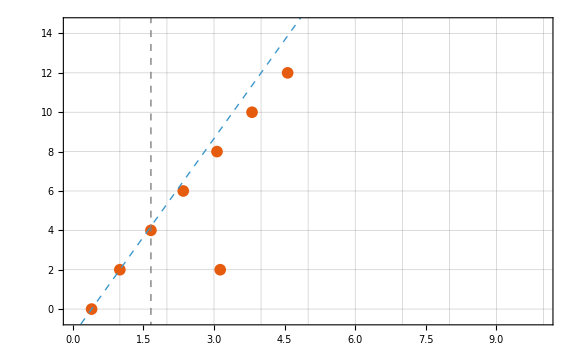

```mathematica
ListPlot[Evaluate[{m2,l}/.DeleteCases[ExtractSpectrumForFig1[0.4,1.66],_?(λ<10^-5/.#&)]],PlotMarkers->{"●", 12},PlotTheme->"Scientific",PlotRange->{{0,10},{-0.5,14.5}},FrameLabel->Evaluate[{Style["",25,FontFamily->"Times New Roman [TMC ]"],Style["",30,FontFamily->"Times New Roman [TMC ]"]}],FrameTicksStyle->Directive[20,FontFamily->"Times New Roman [TMC ]"],ImageSize->Large,GridLines->{Range[1,20,1],Range[0,20,2]}];
Plot[Evaluate[(2/(1-#)(m2-1)+2)&/@{0.4}],{m2,0,20},PlotStyle->Evaluate[{Dashed,Thick}]];
Graphics[{Gray,Dashed,Line[{{1.66,-1},{1.66,20}}]}];
Show[%%%,%%,%]
```

## Monitoring

```mathematica
CheckStatus[]
```

JOBID PARTITION     NAME     USER ST       TIME  NODES NODELIST(REASON)

```mathematica
CheckDigest[]//TableForm
(Length@%-1)//N
```

#fixed_coeff | #sign | #terminateReason
None | 1 | found primal-dual optimal solution
None | 1 | found primal-dual optimal solution
None | 1 | found primal-dual optimal solution
None | 1 | found primal-dual optimal solution
None | 1 | found primal-dual optimal solution
None | 1 | found primal-dual optimal solution
None | 1 | found primal-dual optimal solution
None | 1 | found primal-dual optimal solution
None | 1 | found primal-dual optimal solution
None | 1 | found primal-dual optimal solution
None | 1 | found primal-dual optimal solution
None | 1 | found primal-dual optimal solution
None | 1 | found primal-dual optimal solution

13.

```mathematica
ClusterInfo["private-dpt-bigmem"]
```

Print only nodes in partition private-dpt-bigmem
Hostname       Partition     Node Num_CPU  CPUload  Memsize  Freemem  Joblist
                            State Use/Tot  (15min)     (MB)     (MB)  JobID(JobArrayID) User ...
cpu218   private-dpt-bigmem    idle    0   8    0.00    512000   510459   
cpu219   private-dpt-bigmem    idle    0   8    0.00    512000   510774   
cpu312   private-dpt-bigmem     mix   64 128    0.00*  1024000  1022765  3036976 ricossa *
cpu313   private-dpt-bigmem     mix   64 128    0.00*  1024000  1023972  3036976 ricossa *
             JOBID PARTITION     NAME     USER ST       TIME  NODES NODELIST(REASON)
           3036976 private-d     sdpb  ricossa  R       0:15      2 cpu[312-313]

```mathematica
CancelJob[]
```

<|ExitCode→0,StandardOutput→,StandardError→|>